```mathematica
{"for α=0.55"}
```

```mathematica
Clear["`*"]

Solve[(4π)/9 1/Log[1^2/Λ^2]==0.55,Λ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Λ→-0.28102},{Λ→0.28102}}

```mathematica
Solve[A/Log[1+1/(5*0.281)]==0.55,A]
```

{{A→0.295632}}

{Mine}

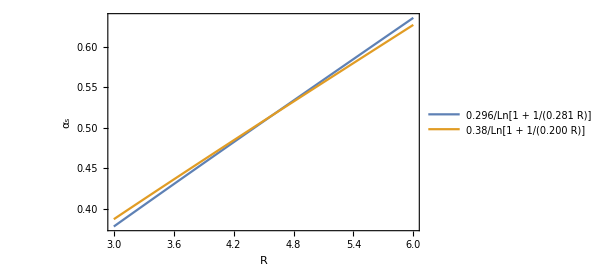

{2004 Da-Heng He}

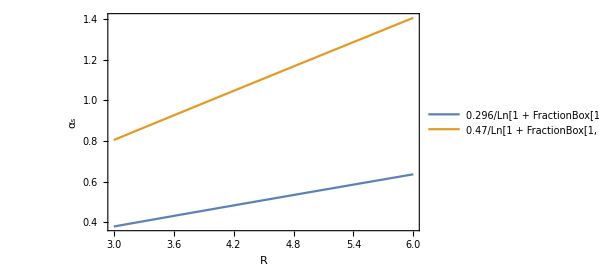

{1983 Meson baryon glueball}

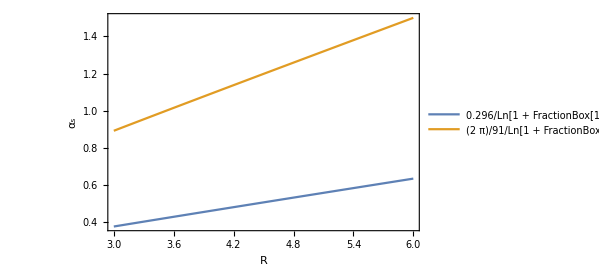

{1980 Heavy quark-antiquark}

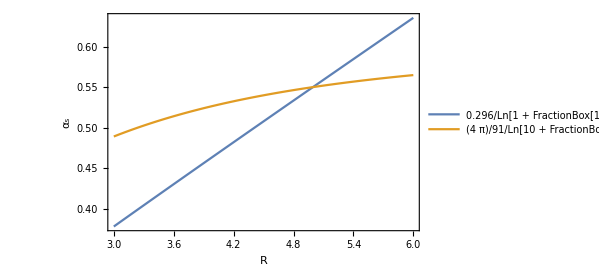

{2013 Magnetic Moment}

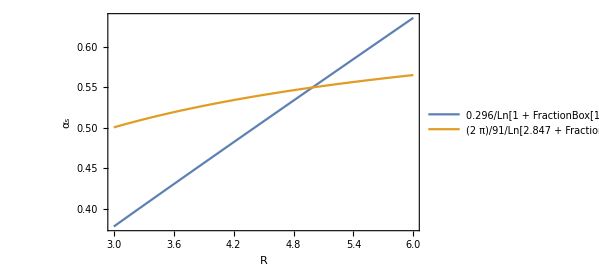

```mathematica
{"Mine"}
Plot[{0.296/Log[1+1/(R*0.281)],0.38/Log[1+1/(R*0.200)]},{R,3,6},Frame->True,FrameLabel->{"R","α_s"},PlotLegends->Placed[{"0.296/Ln[1 + 1/(0.281  R)]","0.38/Ln[1 + 1/(0.200  R)]"},{0.75,0.3}]]
{"2004 Da-Heng He"}
Plot[{0.296/Log[1+1/(R*0.281)],0.47/Log[1+1/(R*0.420)]},{R,3,6},Frame->True,FrameLabel->{"R","α_s"},PlotLegends->Placed[{"0.296/Ln[1 + FractionBox[1, 0.281  R]]","0.47/Ln[1 + FractionBox[1, 0.420  R]]"},{0.75,0.5}]]
{"1983 Meson baryon glueball"}
Plot[{0.296/Log[1+1/(R*0.281)],(2π)/9 1/Log[1+1/(R*0.281)]},{R,3,6},Frame->True,FrameLabel->{"R","α_s"},PlotLegends->Placed[{"0.296/Ln[1 + FractionBox[1, 0.281  R]]","(2  π)/91/Ln[1 + FractionBox[1, 0.281  R]]"},{0.75,0.5}]]
{"1980 Heavy quark-antiquark"}
Plot[{0.296/Log[1+1/(R*0.281)],(4π)/9 1/Log[10+1/(R^2*0.123^2)]},{R,3,6},Frame->True,FrameLabel->{"R","α_s"},PlotLegends->Placed[{"0.296/Ln[1 + FractionBox[1, 0.281  R]]","(4  π)/91/Ln[10 + FractionBox[1, SuperscriptBox[0.123, 2] SuperscriptBox[R, 2]]]"},{0.75,0.3}]]
{"2013 Magnetic Moment"}
Plot[{0.296/Log[1+1/(R*0.281)],(2π)/9 1/Log[2.847+1/(R*0.281)]},{R,3,6},Frame->True,FrameLabel->{"R","α_s"},PlotLegends->Placed[{"0.296/Ln[1 + FractionBox[1, 0.281  R]]","(2  π)/91/Ln[2.847 + FractionBox[1, 0.281  R]]"},{0.75,0.3}]]
```

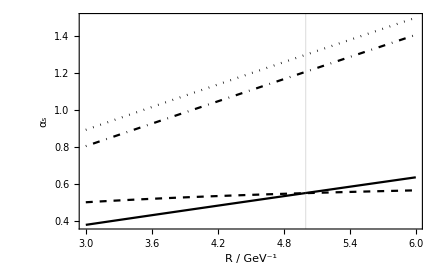

```mathematica
Plot[{0.296/Log[1+1/(R*0.281)],0.47/Log[1+1/(R*0.420)],(2π)/9 1/Log[1+1/(R*0.281)],(2π)/9 1/Log[2.847+1/(R*0.281)]},{R,3,6},GridLines->{{5},{}},Frame->True,FrameLabel->{"R / GeV^-1","α_s"},FrameStyle->Directive[Black,Bold],PlotStyle->{{Black,Ticks},{Black,DotDashed},{Black,Dotted},{Black,Dashed}},LabelStyle->Directive[Black,Bold]]
```